# Band Structure for FCC crystal with free ⅇ

Author1, Author 2, 
Afiliation 
Date of Submission

Here we develop the calculation of the band structure for fcc crystal with free ϵ; remind that: ⅈ , ∇_■ □ (is esc+grad+esc), ∇_■^2 □ (esc+del2+esc)

```mathematica
κ = {kx, ky,kz};
G = {Gx,Gy,Gz};
r = {x,y,z};
u = Exp[ⅈ G.r];
```

```mathematica
-ℏ^2/(2 m) (∇_r^2 u+2 ⅈ κ.∇_r u - κ.κ u)//FullSimplify
```

(ⅇ^(ⅈ (Gx x+Gy y+Gz z)) ((Gx+kx)^2+(Gy+ky)^2+(Gz+kz)^2) ℏ^2)/(2 m)

We need the lattice vector for an fcc crystal:

```mathematica
a1 = a {1/2,1/2,0};
a2 = a{1/2,0,1/2};
a3 = a{0,1/2,1/2};
```

```mathematica
b1 = 2 π (a2 × a3)/(a1.(a2×a3));
b2 = 2 π (a3× a1)/(a1.(a2×a3));
b3 = 2 π (a1 × a2)/(a1.(a2×a3));
```

Now we need to define the G vectors

```mathematica
Gv = m1 b1 +m2 b2 +m3 b3 //FullSimplify
```

{(2 (m1+m2-m3) π)/a,(2 (m1-m2+m3) π)/a,(2 (-m1+m2+m3) π)/a}

```mathematica
G = Table[Gv a/(2 π),{m1,-1,1},{m2,-1,1},{m3,-1,1}]//Flatten//Partition[#,3]&//Sort[#,Norm[#1]<Norm[#2]&]&
```

{{0,0,0},{1,1,1},{1,1,-1},{1,-1,1},{-1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1},{-1,-1,-1},{2,0,0},{0,2,0},{0,0,2},{0,0,-2},{0,-2,0},{-2,0,0},{2,0,-2},{0,2,-2},{2,-2,0},{-2,2,0},{0,-2,2},{-2,0,2},{3,-1,-1},{-1,3,-1},{1,1,-3},{-1,-1,3},{1,-3,1},{-3,1,1}}

We are going to compute the BS along these HSP, these are the high symmetry points:

L →K→U→W→Γ→X→W→L→Γ→K

```mathematica
kp = {
{0.5,0.5,0.5}(*L*), 
{0.75,0.75,0}(*K*),
{1, 0.25, 0.25}(*U*),
{1,0.5,0}(*W*),
{0,0,0}(*Γ*),
{1,0,0}(*X*),
{1,0.5,0}(*W*),
{0.5,0.5,0.5}(*L*), 
{0,0,0}(*Γ*),
{0.75,0.75,0}(*K*),
};
```

```mathematica
div=10;
```

```mathematica
Do[Δk[i]=(kp[[i+1]]-kp[[i]])/(div-1),{i,9}]
```

```mathematica
Δk[1]
```

{0.0277778,0.0277778,-0.0555556}

```mathematica
Δk[2]
```

{0.0277778,-0.0555556,0.0277778}

```mathematica
Δk[9]
```

{0.0833333,0.0833333,0}

### Discretization of path along HSP

```mathematica
n=1
LK =Table[{i Δk[n]//Norm,kp[[n]]+i Δk[n]},{i,0,div-1}]
```

1

{{0.,{0.5,0.5,0.5}},{0.0680414,{0.527778,0.527778,0.444444}},{0.136083,{0.555556,0.555556,0.388889}},{0.204124,{0.583333,0.583333,0.333333}},{0.272166,{0.611111,0.611111,0.277778}},{0.340207,{0.638889,0.638889,0.222222}},{0.408248,{0.666667,0.666667,0.166667}},{0.47629,{0.694444,0.694444,0.111111}},{0.544331,{0.722222,0.722222,0.0555556}},{0.612372,{0.75,0.75,0.}}}

```mathematica
n=2;
KU =Table[{(i Δk[n]//Norm)+LK[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

```mathematica
KU
```

{{0.612372,{0.75,0.75,0.}},{0.680414,{0.777778,0.694444,0.0277778}},{0.748455,{0.805556,0.638889,0.0555556}},{0.816497,{0.833333,0.583333,0.0833333}},{0.884538,{0.861111,0.527778,0.111111}},{0.952579,{0.888889,0.472222,0.138889}},{1.02062,{0.916667,0.416667,0.166667}},{1.08866,{0.944444,0.361111,0.194444}},{1.1567,{0.972222,0.305556,0.222222}},{1.22474,{1.,0.25,0.25}}}

```mathematica
n=3;
UW =Table[{(i Δk[n]//Norm) +KU[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

```mathematica
n=4;
WΓ =Table[{(i Δk[n]//Norm) +UW[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

```mathematica
n=5;
ΓX =Table[{(i Δk[n]//Norm) +WΓ[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

```mathematica
n=6;
XW =Table[{(i Δk[n]//Norm) +ΓX[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

```mathematica
n=7;
WL =Table[{(i Δk[n]//Norm) +XW[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

```mathematica
n=8;
LΓ =Table[{(i Δk[n]//Norm) +WL[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

```mathematica
n=9;
ΓK =Table[{(i Δk[n]//Norm) +LΓ[[-1,1]],kp[[n]]+i Δk[n]},{i,0,div-1}];
```

### Computing the bands

Let’s compute the bands along the HSP, here we will use only for visualization a conversion factor n = 1 and the fermi level ef=0\
-Graphics-

For each path

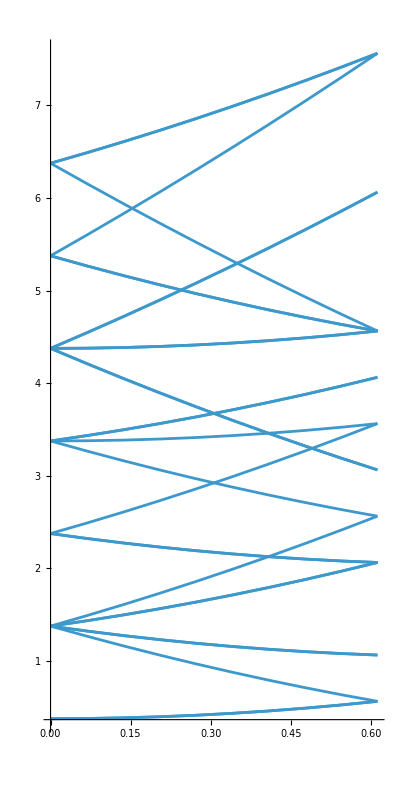

```mathematica
n=1;
ef=0;
Do[
bLK[i]=LK//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbLK[i]=ListPlot[bLK[i],Joined->True],{i,G//Length}
];
pathLK=Show[Table[gbLK[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

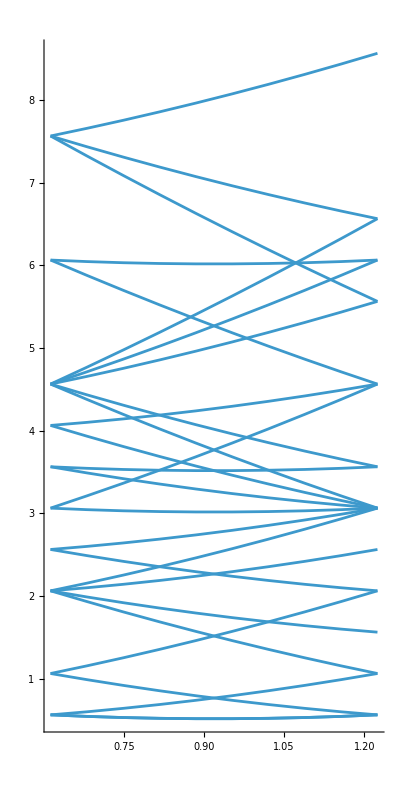

```mathematica
Do[
bKU[i]=KU//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbKU[i]=ListPlot[bKU[i],Joined->True],{i,G//Length}
];
pathKU=Show[Table[gbKU[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

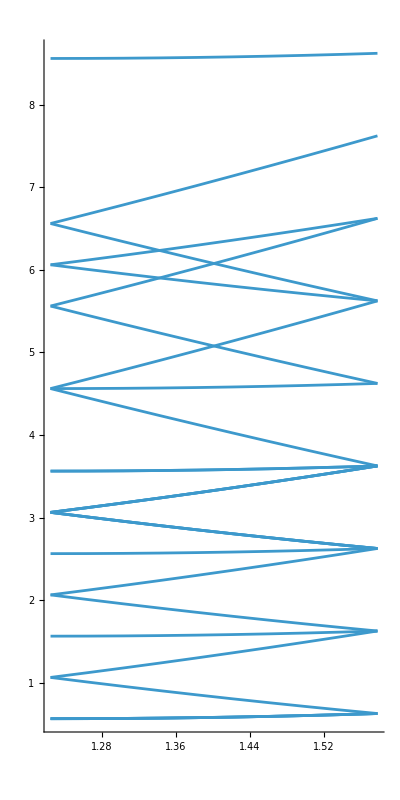

```mathematica
Do[
bUW[i]=UW//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbUW[i]=ListPlot[bUW[i],Joined->True],{i,G//Length}
];
pathUW=Show[Table[gbUW[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

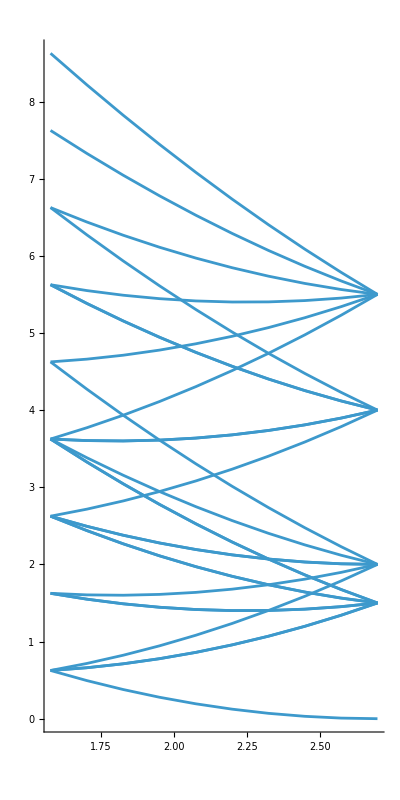

```mathematica
Do[
bWΓ[i]=WΓ//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbWΓ[i]=ListPlot[bWΓ[i],Joined->True],{i,G//Length}
];
pathWΓ=Show[Table[gbWΓ[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

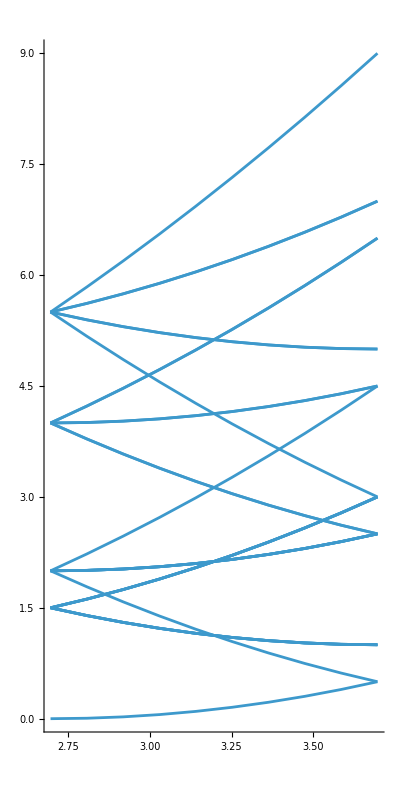

```mathematica
Do[
bΓX[i]=ΓX//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbΓX[i]=ListPlot[bΓX[i],Joined->True],{i,G//Length}
];
pathΓX=Show[Table[gbΓX[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

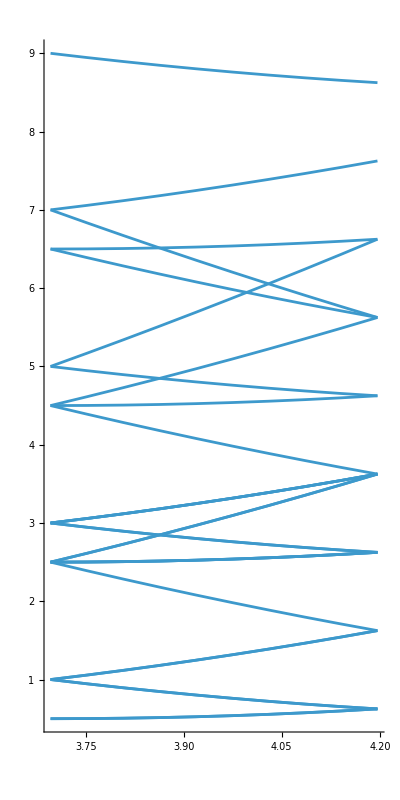

```mathematica
Do[
bXW[i]=XW//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbXW[i]=ListPlot[bXW[i],Joined->True],{i,G//Length}
];
pathXW=Show[Table[gbXW[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

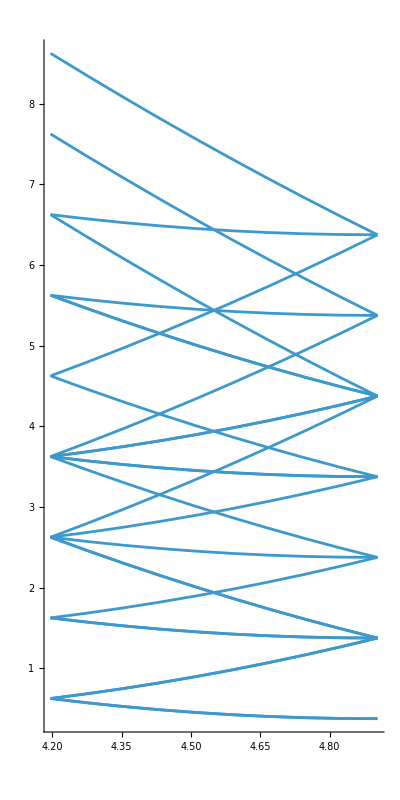

```mathematica
Do[
bWL[i]=WL//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbWL[i]=ListPlot[bWL[i],Joined->True],{i,G//Length}
];
pathWL=Show[Table[gbWL[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

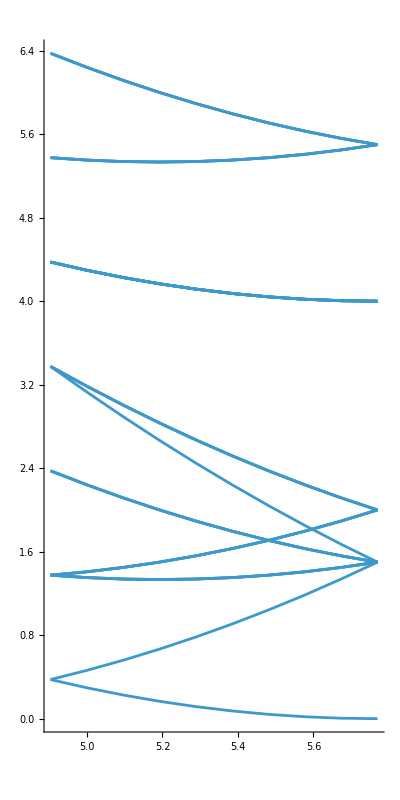

```mathematica
Do[
bLΓ[i]=LΓ//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbLΓ[i]=ListPlot[bLΓ[i],Joined->True],{i,G//Length}
];
pathLΓ=Show[Table[gbLΓ[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

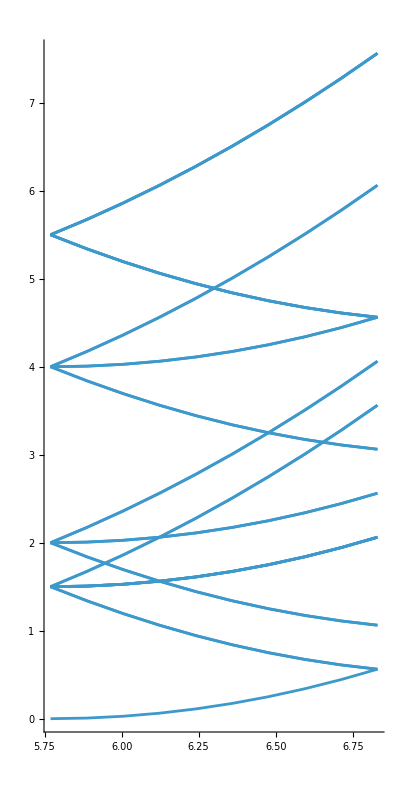

```mathematica
Do[
bΓK[i]=ΓK//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbΓK[i]=ListPlot[bΓK[i],Joined->True],{i,G//Length}
];
pathΓK=Show[Table[gbΓK[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

Band only appear with periodic boundary conditions, basically when we have a Crystal

### The plot of the band structure for fcc crystal

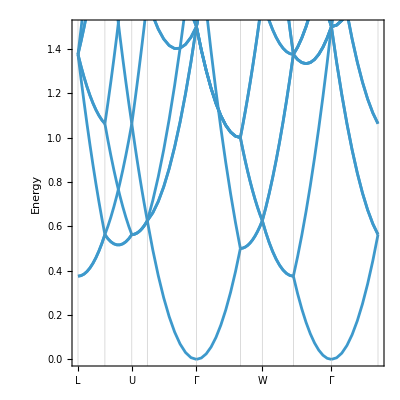

```mathematica
Show[{pathLK,pathKU,pathUW,pathWΓ,pathΓX,pathXW,pathWL,pathLΓ,pathΓK},PlotRange->{{0,ΓK[[-1,1]]},{0,1.5}},AspectRatio->1,GridLines->{{0,LK[[-1,1]],KU[[-1,1]],UW[[-1,1]],WΓ[[-1,1]],ΓX[[-1,1]],XW[[-1,1]],WL[[-1,1]],LΓ[[-1,1]],ΓK[[-1,1]]},None},Axes->None,FrameTicks->{{Automatic,Automatic},{{{0,"L"},{LK[[-1,1]],"K"},{KU[[-1,1]],"U"},{UW[[-1,1]],"W"},{WΓ[[-1,1]],"Γ"},{ΓX[[-1,1]],"X"},{XW[[-1,1]],"W"},{WL[[-1,1]],"L"},{LΓ[[-1,1]],"Γ"},{ΓK[[-1,1]],"K"}},None}},BaseStyle->{FontFamily->"Helvetica",FontSize->15},Frame->True,FrameLabel->{"","Energy"}]
```

### The fcc crystal with free electron and 3 valence electrons.

the band structure will remain the same, the one that gonna change is the fermi level.

Where is the fermi level?

Let’s consider that for an fcc crystal with 1 atom per primitive cell has 3 valence electrons.
Keep in mind that the volume of the primitive cell (PC) is a0^3/4,
where a0 is the lattice parameter of the UC (cubic)

```mathematica
En==ℏ^2/(2 m)k^2
```

then

```mathematica
dEn=ℏ^2/(2 m)k^2 dk
```

```mathematica
dk/dEn==m/(ℏ^2 k)
```

The electron density of states, considering the two spins states of 3 is:

```mathematica
g[En]dEn==2  (4 π k^2)/((2 π)/L)^3 dk
```

```mathematica
g[En_]:=(2  (4 π k^2)/((2 π)/L)^3 dk/dEn/.dk/dEn->m/(ℏ^2 k))/.k->√(2 m En/ℏ^2) //PowerExpand
```

If we integrate g[En] form 0 to Ef, we should get the total num er of valence electrons.

```mathematica
Clear[ef];
```

```mathematica
Integrate[g[En],{En,0,ef}]
```

(2 √2 ef^(3/2) L^3 m^(3/2))/(3 π^2 ℏ^3)

```mathematica
Solve[(2 √2 ef^(3/2) L^3 m^(3/2))/(3 π^2 ℏ^3)==N,ef]
```

{{ef→1/2 3^(2/3) π^(4/3) ((N ℏ^3)/(L^3 m^(3/2)))^(2/3)}}

We also have to keep in mind that L = a0 (1/4)^(1/3) (L is lenght is the volume [a1.(a2 (×a3)])^(1/3) and for the case of Al=fcc, N=3, have to rescale

```mathematica
efermi=(1/2 3^(2/3) π^(4/3) ((N ℏ^3)/(L^3 m^(3/2)))^(2/3))/(2 π/a0)^2/.{L->a0(1/4)^(1/3),N->3,m->1,ℏ->1}//PowerExpand//N
```

0.635348

The factor  (2 π/a0)^2 is to scale the units we are using (look G vector) in our band structure. 
Remember that k and G vectors where scaled as 1/(2 π/a0)

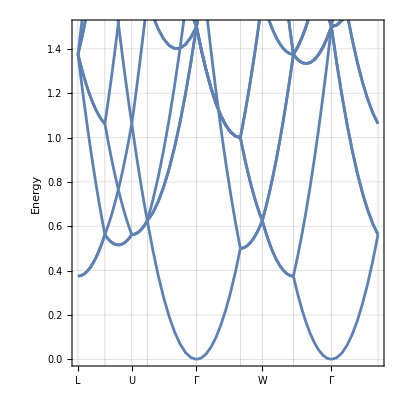

```mathematica
Show[{pathLK, pathKU,pathUW, pathWΓ,pathΓX,pathXW,pathWL,pathLΓ,pathΓK},
PlotRange->{{0,ΓK[[-1,1]]},{0,1.5}},
AspectRatio->1,
GridLines->{
{0,LK[[-1,1]],
KU[[-1,1]],
UW[[-1,1]],
WΓ[[-1,1]],
ΓX[[-1,1]],
XW[[-1,1]],
WL[[-1,1]],
LΓ[[-1,1]],
ΓK[[-1,1]]},efermi},
Axes->None,
FrameTicks->{{Automatic,Automatic},
{{{0,"L"},{LK[[-1,1]],"K"},{KU[[-1,1]],"U"},{UW[[-1,1]],"W"},{WΓ[[-1,1]],"Γ"},{ΓX[[-1,1]],"X"},
{XW[[-1,1]],"W"},{WL[[-1,1]],"L"},{LΓ[[-1,1]],"Γ"},
{ΓK[[-1,1]],"K"}},None}},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Frame->True,FrameLabel->{"","Energy"}]
```

### The fcc crystal with free electron and 3 valence electrons.

the band structure will remain the same, the one that gonna change is the fermi level.

Where is the fermi level?

Let’s consider that for an fcc crystal with 1 atom per primitive cell has 3 valence electrons.
Keep in mind that the volume of the primitive cell (PC) is a0^3/4,
where a0 is the lattice parameter of the UC (cubic)

```mathematica
En==ℏ^2/(2 m)k^2
```

then

```mathematica
dEn=ℏ^2/(2 m)k^2 dk
```

```mathematica
dk/dEn==m/(ℏ^2 k)
```

The electron density of states, considering the two spins states of 3 is:

```mathematica
g[En]dEn==2  (4 π k^2)/((2 π)/L)^3 dk
```

```mathematica
g[En_]:=(2  (4 π k^2)/((2 π)/L)^3 dk/dEn/.dk/dEn->m/(ℏ^2 k))/.k->√(2 m En/ℏ^2) //PowerExpand
```

If we integrate g[En] form 0 to Ef, we should get the total num er of valence electrons.

```mathematica
Clear[ef];
```

```mathematica
Integrate[g[En],{En,0,ef}]
```

(2 √2 ef^(3/2) L^3 m^(3/2))/(3 π^2 ℏ^3)

```mathematica
Solve[(2 √2 ef^(3/2) L^3 m^(3/2))/(3 π^2 ℏ^3)==N,ef]
```

{{ef→1/2 3^(2/3) π^(4/3) ((N ℏ^3)/(L^3 m^(3/2)))^(2/3)}}

We also have to keep in mind that L = a0 (1/4)^(1/3) (L is lenght is the volume [a1.(a2 (×a3)])^(1/3) and for the case of Al=fcc, N=3, have to rescale

```mathematica
efermi=(1/2 3^(2/3) π^(4/3) ((N ℏ^3)/(L^3 m^(3/2)))^(2/3))/(2 π/a0)^2/.{L->a0(1/4)^(1/3),N->3,m->1,ℏ->1}//PowerExpand//N
```

0.635348

The factor  (2 π/a0)^2 is to scale the units we are using (look G vector) in our band structure. 
Remember that k and G vectors where scaled as 1/(2 π/a0)

```mathematica
Show[{pathLK, pathKU,pathUW, pathWΓ,pathΓX,pathXW,pathWL,pathLΓ,pathΓK},
PlotRange->{{0,ΓK[[-1,1]]},{0,1.5}},
AspectRatio->1,
GridLines->{
{0,LK[[-1,1]],
KU[[-1,1]],
UW[[-1,1]],
WΓ[[-1,1]],
ΓX[[-1,1]],
XW[[-1,1]],
WL[[-1,1]],
LΓ[[-1,1]],
ΓK[[-1,1]]},efermi},
Axes->None,
FrameTicks->{{Automatic,Automatic},
{{{0,"L"},{LK[[-1,1]],"K"},{KU[[-1,1]],"U"},{UW[[-1,1]],"W"},{WΓ[[-1,1]],"Γ"},{ΓX[[-1,1]],"X"},
{XW[[-1,1]],"W"},{WL[[-1,1]],"L"},{LΓ[[-1,1]],"Γ"},
{ΓK[[-1,1]],"K"}},None}},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Frame->True,FrameLabel->{"","Energy"}]
```

-Graphics-

### The band structure for Al -fcc in eV using the free electron model a_0=4.05 Å that is 7.6534 bohr.

The fermi level E_f is:

```mathematica
efermi = 1/2 3^(2/3) π^(4/3) ((N ℏ^3)/(L^3 m^(3/2)))^(2/3) 27.2114/.{L->a0(1/4)^(1/3),N->3,m->1,ℏ->1}/.a0->7.6534
```

11.6524

### Computing the bands

Let’s compute the bands along the HSP, here we will use only for visualization a conversion factor n = 1 and the fermi level ef=0\
-Graphics-

For each path

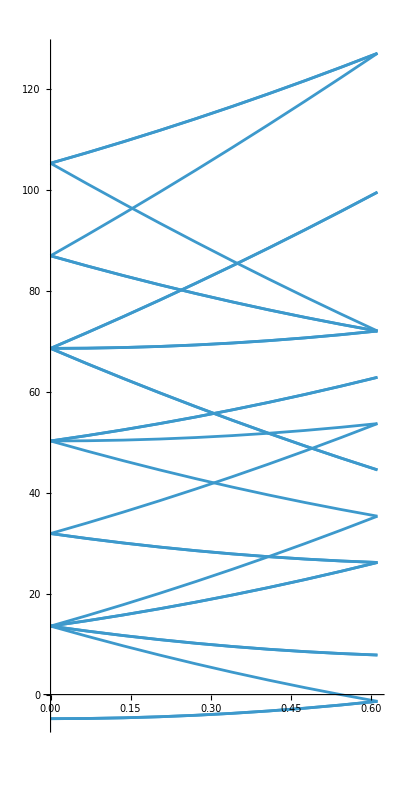

```mathematica
n=27.2114 (2 π/7.6534)^2;
ef=efermi;
Do[
bLK[i]=LK//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbLK[i]=ListPlot[bLK[i],Joined->True],{i,G//Length}
];
pathLK=Show[Table[gbLK[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

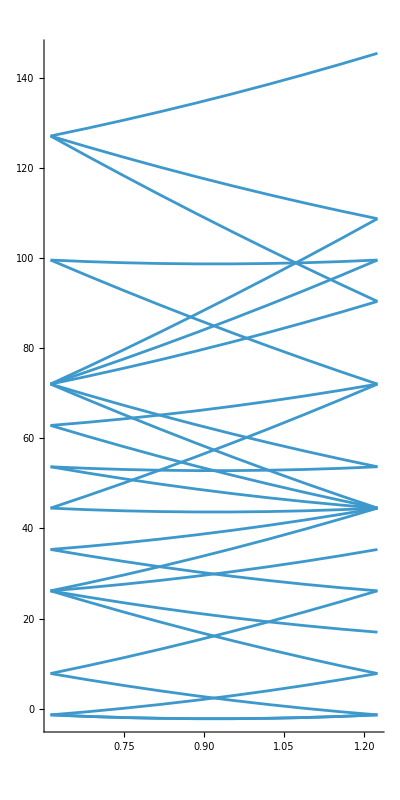

```mathematica
Do[
bKU[i]=KU//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbKU[i]=ListPlot[bKU[i],Joined->True],{i,G//Length}
];
pathKU=Show[Table[gbKU[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

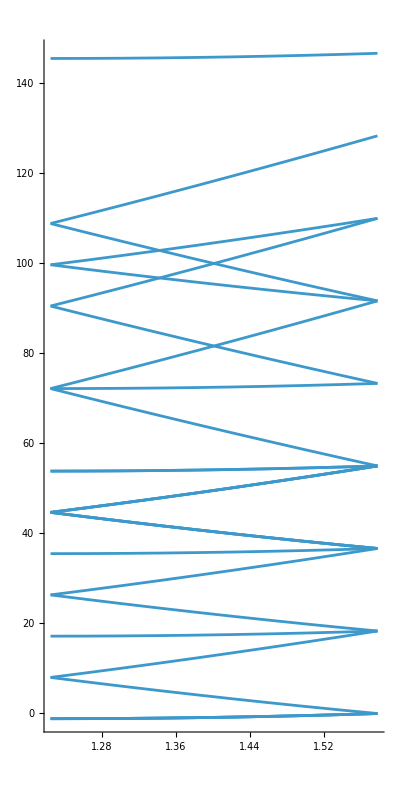

```mathematica
Do[
bUW[i]=UW//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbUW[i]=ListPlot[bUW[i],Joined->True],{i,G//Length}
];
pathUW=Show[Table[gbUW[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

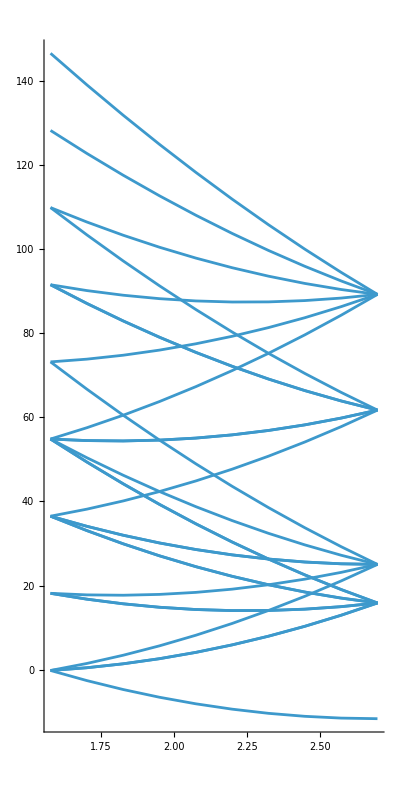

```mathematica
Do[
bWΓ[i]=WΓ//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbWΓ[i]=ListPlot[bWΓ[i],Joined->True],{i,G//Length}
];
pathWΓ=Show[Table[gbWΓ[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

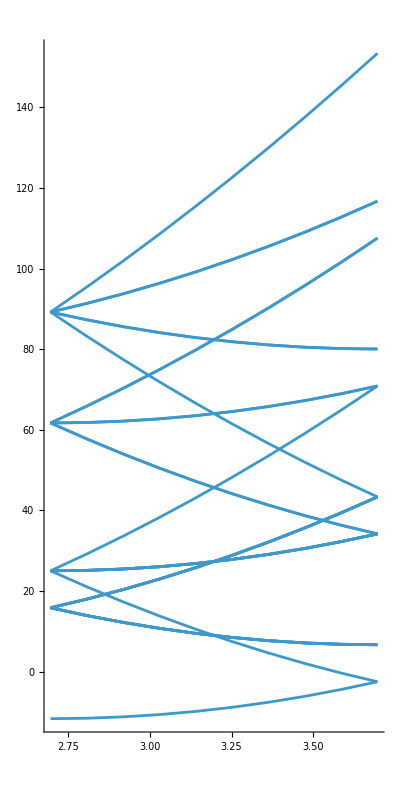

```mathematica
Do[
bΓX[i]=ΓX//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbΓX[i]=ListPlot[bΓX[i],Joined->True],{i,G//Length}
];
pathΓX=Show[Table[gbΓX[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

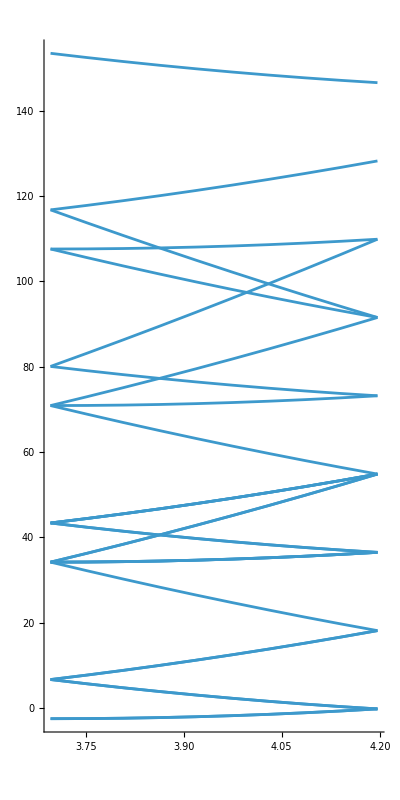

```mathematica
Do[
bXW[i]=XW//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbXW[i]=ListPlot[bXW[i],Joined->True],{i,G//Length}
];
pathXW=Show[Table[gbXW[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

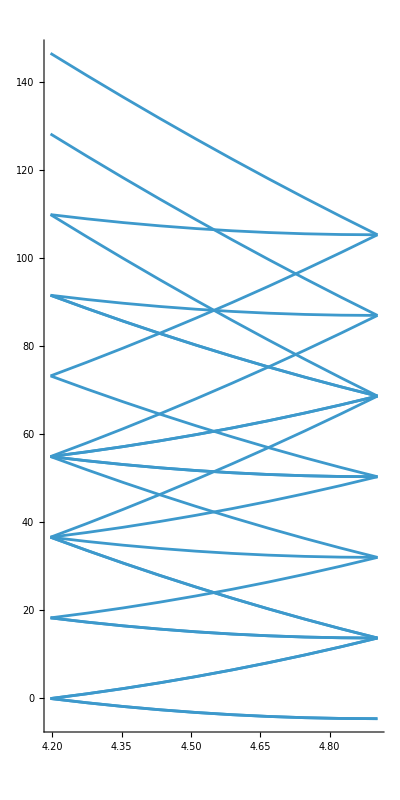

```mathematica
Do[
bWL[i]=WL//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbWL[i]=ListPlot[bWL[i],Joined->True],{i,G//Length}
];
pathWL=Show[Table[gbWL[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

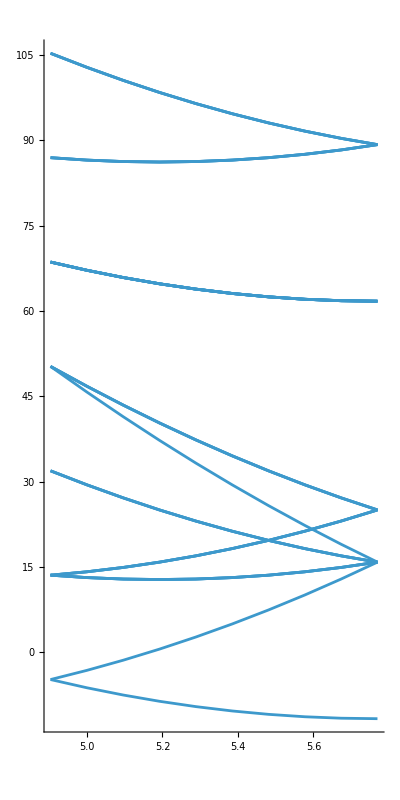

```mathematica
Do[
bLΓ[i]=LΓ//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbLΓ[i]=ListPlot[bLΓ[i],Joined->True],{i,G//Length}
];
pathLΓ=Show[Table[gbLΓ[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

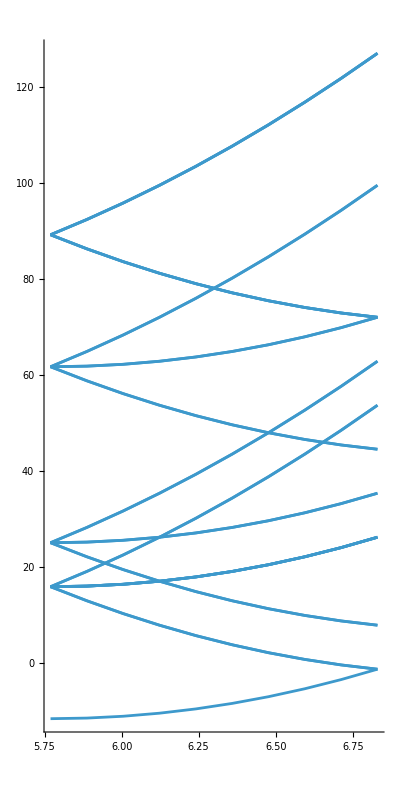

```mathematica
Do[
bΓK[i]=ΓK//Map[{#[[1]],1/2 n(#[[2]]+G[[i]]).(#[[2]]+G[[i]])-ef}&,#]&;
gbΓK[i]=ListPlot[bΓK[i],Joined->True],{i,G//Length}
];
pathΓK=Show[Table[gbΓK[i],{i,G//Length}],PlotRange->All,AspectRatio->2]
```

Band only appear with periodic boundary conditions, basically when we have a Crystal

### The plot of the band structure for AL fcc crystal within the free electron model

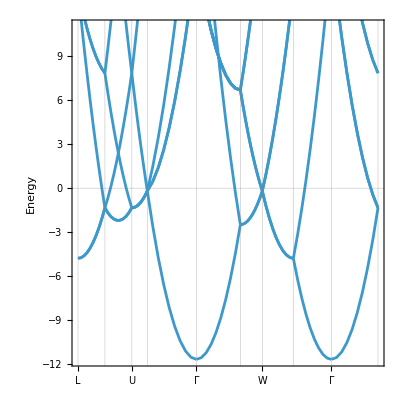

```mathematica
Show[{pathLK,pathKU,pathUW,pathWΓ,pathΓX,pathXW,pathWL,pathLΓ,pathΓK},PlotRange->{{0,ΓK[[-1,1]]},{-ef,11}},AspectRatio->1,GridLines->{{0,LK[[-1,1]],KU[[-1,1]],UW[[-1,1]],WΓ[[-1,1]],ΓX[[-1,1]],XW[[-1,1]],WL[[-1,1]],LΓ[[-1,1]],ΓK[[-1,1]]},{0}},Axes->None,FrameTicks->{{Automatic,Automatic},{{{0,"L"},{LK[[-1,1]],"K"},{KU[[-1,1]],"U"},{UW[[-1,1]],"W"},{WΓ[[-1,1]],"Γ"},{ΓX[[-1,1]],"X"},{XW[[-1,1]],"W"},{WL[[-1,1]],"L"},{LΓ[[-1,1]],"Γ"},{ΓK[[-1,1]],"K"}},None}},BaseStyle->{FontFamily->"Helvetica",FontSize->15},Frame->True,FrameLabel->{"","Energy"}]
```

in the  ssame notebook  we add the band structure for a bcc crystal using the free

## The band structure for a bcc crystal using the free ⅇ model, then apply for the case of Na-bcc that has 1 valance ⅇ.

Use the BBC lattice parameter

Use the following path along the HSP:

Γ → H→N→Γ→P→H

```mathematica
kp={
{0,0,0},(*Γ*)
{0.5,-0.5,0.5},(*H*)
{0,0,0.5},(*N*)
{0,0,0},(*Γ*)
{0.25,0.25,0.25},(*P*)
{0.5,-0.5,0.5}(*H*)
}
```